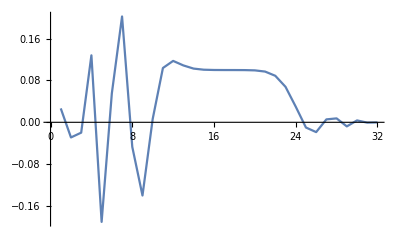

```mathematica
Table[nsol[[k]]'[10],{k,1,n}]//ListLinePlot
```

```mathematica
Animate[
ListLinePlot[
Table[
nsol[[j]]'[tt],{j,1,n}
],Mesh->All,PlotRange->{All,{-1,1}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Velocity"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->10]
```

```mathematica
Animate[
ListLinePlot[
Table[
0.5(
(nsol[[j]][tt])^2+(nsol[[j]]'[tt]-nsol[[j-1]]'[tt])^2 
)+ (α/3)(nsol[[j]]'[tt]-nsol[[j-1]]'[tt])^3,{j,2,n}
],Mesh->All,PlotRange->{All,{0,1.75}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Velocity"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->10]//Inactivate
```

$Aborted[]

```mathematica
list=Table[nsol[[j]][100],{j,1,32}];
```

0.-0.0715825 Sin[t]-0.0238608 Sin[3 t]-0.0143165 Sin[5 t]-0.0102261 Sin[7 t]-0.00795361 Sin[9 t]-0.0065075 Sin[11 t]-0.00550635 Sin[13 t]-0.00477217 Sin[15 t]-0.00421074 Sin[17 t]-0.0037675 Sin[19 t]-0.00340869 Sin[21 t]-0.00311228 Sin[23 t]-0.0028633 Sin[25 t]-0.0026512 Sin[27 t]-0.00246836 Sin[29 t]

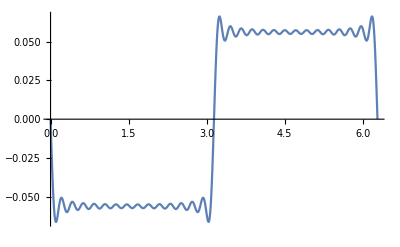

```mathematica
FourierSinSeries[list,t,30][[1]]
Plot[%,{t,0,2π}]
```